## Qx this part is to compute Qx0 and Qx1

```mathematica
(*p=ⅇ^(β (J Cos[θ1-θ2]+μ (Cos[θ1]+Cos[θ2]) Ex))
Normal[Series[p,{Ex,0,3}]]*)
```

```mathematica
(*p0=Normal[Series[p,{Ex,0,0}]]
p1=Normal[Series[p,{Ex,0,1}]]-p0
p2=Normal[Series[p,{Ex,0,2}]]-p1-p0
p3=Normal[Series[p,{Ex,0,3}]]-p2-p1-p0*)
```

```mathematica
(*q0=Integrate[p0,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

```mathematica
(*4 π^2 BesselI[0,J β];*)
```

```mathematica
(*q1=Integrate[p1,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

```mathematica
(*q2=Integrate[p2,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

```mathematica
(*2 Ex^2 π^2 β^2 μ^2 (BesselI[0,J β]+BesselI[1,J β]);*)
```

```mathematica
(*q3=Integrate[p3,{θ1,0,2Pi},{θ2,0,2Pi}]*)
```

It seems odd terms are all zero.

```mathematica
(*q=q0+q1+q2+q3;
Normal[Series[1/q D[q,Ex],{Ex,0,3}]]*)
```

```mathematica
(*(Ex β^2 μ^2 (BesselI[0,J β]+BesselI[1,J β]))/BesselI[0,J β]-(Ex^3 β^4 μ^4 (BesselI[0,J β]+BesselI[1,J β])^2)/(2 BesselI[0,J β]^2);*)
```

So

```mathematica
(*Qx0=0;
Qx1=β^2 μ^2+(β^2 μ^2 BesselI[1,J β])/BesselI[0,J β];*)
```

## test for F(theta1,theta 2)

need to solve possion function

note bmu = β μ and bJ= β J

(∂^2 ψ)/(∂theta1^2)+(∂^2 ψ)/(∂theta2^2)=(-bmu(Cos[theta1]+Cos[theta2]+QX))Exp[bJ Cos[theta1-theta2]+bmu Ε (Cos[theta1]+Cos[theta2])];

```mathematica
Qx=Qx0+Qx1 Ε;
Qx0=0;
F[theta1_,theta2_]:=(-bmu(Cos[theta1]+Cos[theta2])+Qx)Exp[bJ Cos[theta1-theta2]+bmu Ε (Cos[theta1]+Cos[theta2])]
F0=Normal[Series[F[theta1,theta2],{Ε,0,0}]]//Simplify
F1=(Normal[Series[F[theta1,theta2],{Ε,0,1}]]-F0)//Simplify
```

-bmu ⅇ^(bJ Cos[theta1-theta2]) (Cos[theta1]+Cos[theta2])

ⅇ^(bJ Cos[theta1-theta2]) Ε (Qx1-bmu^2 Cos[theta1]^2-2 bmu^2 Cos[theta1] Cos[theta2]-bmu^2 Cos[theta2]^2)

```mathematica
Qy=Qy0+Qy1 Ε;
Qy0=0;
F[theta1_,theta2_]:=(-bmu(Sin[theta1]+Sin[theta2])+Qy)Exp[bJ Cos[theta1-theta2]+bmu Ε ( Sin[theta1]+Sin[theta2])]
F0=Normal[Series[F[theta1,theta2],{Ε,0,0}]]//Simplify
F1=(Normal[Series[F[theta1,theta2],{Ε,0,1}]]-F0)//Simplify
```

-bmu ⅇ^(bJ Cos[theta1-theta2]) (Sin[theta1]+Sin[theta2])

ⅇ^(bJ Cos[theta1-theta2]) Ε (Qy1-bmu^2 Sin[theta1]^2-2 bmu^2 Sin[theta1] Sin[theta2]-bmu^2 Sin[theta2]^2)

add one more expansion

```mathematica
Exp[bJ Cos[theta1-theta2]]=∑_(j=0)^N (bJ)^j/j! Cos[theta1-theta2]^j ;
```

Set::write: Tag Exp in Exp[bJ Cos[theta1-theta2]] is Protected.

then we have

## Set up

### Expressions

#### vE

```mathematica
F0[j_,theta1_,theta2_]:=(bJ)^j/j! Cos[theta1-theta2]^j (Qx0-bmu(Cos[theta1]+Cos[theta2]))
Qx0=0;
F1[j_,theta1_,theta2_]:=(bJ)^j/j!Cos[theta1-theta2]^j(Qx1-bmu^2(Cos[theta1]+Cos[theta2])^2+Qx0 bmu(Cos[theta1]+Cos[theta2]))
```

```mathematica
H0[0,j_,theta1_]:=1/(2Pi)Integrate[F0[j,theta1,theta2],{theta2,0,2Pi}]
H0c[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H0s[n_,j_,theta1_]:=1/Pi Integrate[F0[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

IOcch means:∫_0^(2 π) H0c Cosh[2 Pi-xi]ⅆxi  0CCH etc.. and 0 means zero order of Ε

```mathematica
I0cch[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0csh[n_,j_,theta1_]:=Integrate[H0c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I0sch[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I0ssh[n_,j_,theta1_]:=Integrate[H0s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

```mathematica
F0s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0sch[n,j,2Pi]+1/(2n)I0ssh[n,j,2Pi]
F0c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I0cch[n,j,2Pi]+1/(2n)I0csh[n,j,2Pi]
```

```mathematica
E0s[n_,j_]:=F0s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0ssh[n,j,2Pi]
E0c[n_,j_]:=F0c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I0csh[n,j,2Pi]
```

Note the 0 of  A0C(A_0(θ1))  here means zero order of Ε
A0c[0,j,theta1] here is A_0(θ_1) in steven’s sol, this part could be include in ∑_(n=1)^∞ A_n_c Cos(nθ2) so it could start with n=0 i.e. ∑_(n=0)^∞ A_n_c Cos(nθ2) since Cos(nθ2) = 1 for n = 0;

```mathematica
A0c[0,j_,theta1_]:=Integrate[H0[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A0s[0,j_,theta1_]:=0
A0s[n_,j_,theta1_]:=E0s[n,j]Sinh[n theta1]+F0s[n,j]Cosh[n theta1]+1/n I0ssh[n,j,theta1]
A0c[n_,j_,theta1_]:=E0c[n,j]Sinh[n theta1]+F0c[n,j]Cosh[n theta1]+1/n I0csh[n,j,theta1]
```

```mathematica
dA0c[0,j_,theta1_]:=Integrate[H0[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H0[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA0s[0,j_,theta1_]:=0
dA0s[n_,j_,theta1_]:=n E0s[n,j]Cosh[n theta1]+n F0s[n,j]Sinh[n theta1]+I0sch[n,j,theta1]
dA0c[n_,j_,theta1_]:=n E0c[n,j]Cosh[n theta1]+n F0c[n,j]Sinh[n theta1]+I0cch[n,j,theta1]
```

```mathematica
pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

```mathematica
(*pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify*)
```

```mathematica
(*pv20[bJx_,bmux_,theta1_,theta2_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{Qx0->0,bJ->bJx,bmu->bmux},{n,1,nmax},{j,0,jmax}]*)
```

```mathematica
?pv20
```

Global`pv20

pv20[bJx_,bmux_,xi_,xj_]:=∑_(n=1)^nmax ∑_(j=0)^jmax (n A0s[n,j,theta1] Cos[n theta2]-n A0c[n,j,theta1] Sin[n theta2]/.{bJ→bJx,bmu→bmux,theta1→xi,theta2→xj})

#### vEE

```mathematica
H1[0,j_,theta1_]:=1/(2Pi)Integrate[F1[j,theta1,theta2],{theta2,0,2Pi}]
H1c[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Cos[n theta2],{theta2,0,2Pi}]
H1s[n_,j_,theta1_]:=1/Pi Integrate[F1[j,theta1,theta2]Sin[n theta2],{theta2,0,2Pi}]
```

```mathematica
I1cch[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1csh[n_,j_,theta1_]:=Integrate[H1c[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
I1sch[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Cosh[n(theta1-xi)],{xi,0,theta1}]
I1ssh[n_,j_,theta1_]:=Integrate[H1s[n,j,xi]Sinh[n(theta1-xi)],{xi,0,theta1}]
```

small question here, I1CCH integrate along theta1?

```mathematica
F1s[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1sch[n,j,2Pi]+1/(2n)I1ssh[n,j,2Pi]
F1c[n_,j_]:=Sinh[2Pi n]/(2n)/(1-Cosh[2Pi n])I1cch[n,j,2Pi]+1/(2n)I1csh[n,j,2Pi]
E1s[n_,j_]:=F1s[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1ssh[n,j,2Pi]
E1c[n_,j_]:=F1c[n,j](1-Cosh[2Pi n])/Sinh[2Pi n]-1/n/Sinh[2Pi n]I1csh[n,j,2Pi]
```

```mathematica
A1c[0,j_,theta1_]:=Integrate[H1[0,j,xi](theta1-xi),{xi,0,theta1}]-theta1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
A1s[0,j_,theta1_]:=0
A1s[n_,j_,theta1_]:=E1s[n,j]Sinh[n theta1]+F1s[n,j]Cosh[n theta1]+1/n I1ssh[n,j,theta1]
A1c[n_,j_,theta1_]:=E1c[n,j]Sinh[n theta1]+F1c[n,j]Cosh[n theta1]+1/n I1csh[n,j,theta1]
dA1c[0,j_,theta1_]:=Integrate[H1[0,j,xi],{xi,0,theta1}]-1/(2Pi)Integrate[H1[0,j,xi](2Pi-xi),{xi,0,2Pi}]
dA1s[0,j_,theta1_]:=0
dA1s[n_,j_,theta1_]:=n E1s[n,j]Cosh[n theta1]+n F1s[n,j]Sinh[n theta1]+I1sch[n,j,theta1]
dA1c[n_,j_,theta1_]:=n E1c[n,j]Cosh[n theta1]+n F1c[n,j]Sinh[n theta1]+I1cch[n,j,theta1]
```

```mathematica
pv11[bJx_,bmux_,xi_,xj_]:=Sum[dA1s[n,j,theta1]Sin[n theta2]+dA1c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv21[bJx_,bmux_,xi_,xj_]:=Sum[n A1s[n,j,theta1]Cos[n theta2]-n A1c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]
```

```mathematica
(*pv10[bJx_,bmux_,xi_,xj_]:=Sum[dA0s[n,j,theta1]Sin[n theta2]+dA0c[n,j,theta1]Cos[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,0,nmax},{j,0,jmax}]
pv20[bJx_,bmux_,xi_,xj_]:=Sum[n A0s[n,j,theta1]Cos[n theta2]-n A0c[n,j,theta1]Sin[n theta2]/.{bJ->bJx,bmu->bmux,theta1->xi,theta2->xj},{n,1,nmax},{j,0,jmax}]*)
```

### Export (is commented out, no need to compute)

#### zero order

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0x.xls",Table[{j,H0[0,j,theta1]},{j,0,10}]];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0cx.xls",Table[{n,j,H0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0sx.xls",Table[{n,j,H0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Timing[Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cchx.xls",Table[{n,j,I0cch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify]];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0schx.xls",Table[{n,j,I0sch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cshx.xls",Table[{n,j,I0csh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0sshx.xls",Table[{n,j,I0ssh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0sx.xls",Table[{n,j,F0s[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0cx.xls",Table[{n,j,F0c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0sx.xls",Table[{n,j,E0s[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0cx.xls",Table[{n,j,E0c[n,j]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx0.xls",Table[{n,j,A0c[0,j,theta1]},{n,0,0},{j,0,10}]//Simplify];
Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx.xls",Table[{n,j,A0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0sx.xls",Table[{n,j,A0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx.xls",Table[{n,j,dA0c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx0.xls",Table[{n,j,dA0c[0,j,theta1]},{n,0,0},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0sx.xls",Table[{n,j,dA0s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

#### first order

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1x.xls",Table[{j,H1[0,j,theta1]},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1cx.xls",Table[{n,j,H1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1sx.xls",Table[{n,j,H1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Timing[Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cchx.xls",Table[{n,j,I1cch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify]]*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1schx.xls",Table[{n,j,I1sch[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cshx.xls",Table[{n,j,I1csh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sshx.xls",Table[{n,j,I1ssh[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["/usr/users/weisongl/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1cx0.xls",Table[{j,A1c[0,j,theta1]},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1cx.xls",Table[{n,j,A1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1sx.xls",Table[{n,j,A1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["/usr/users/weisongl/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1cx0.xls",Table[{j,dA1c[0,j,theta1]},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1cx.xls",Table[{n,j,dA1c[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

```mathematica
(*Export["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1sx.xls",Table[{n,j,dA1s[n,j,theta1]},{n,1,5},{j,0,10}]//Simplify];*)
```

### Import zero order

#### H0ns

Fully Check for H0

```mathematica
H0x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0x.xls"],1];
Table[H0[0,j_,xi_]:=ToExpression[H0x[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0cx.xls"],1];
Table[H0c[n_,j_,xi_]:=ToExpression[H0cx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H0sx.xls"],1];
Table[H0s[n_,j_,xi_]:=ToExpression[H0sx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### I0cch

```mathematica
I0cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cchx.xls"],1];
Table[I0cch[n_,j_,xi_]:=ToExpression[I0cchx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0schx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0schx.xls"],1];
Table[I0sch[n_,j_,xi_]:=ToExpression[I0schx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0cshx.xls"],1];
Table[I0csh[n_,j_,xi_]:=ToExpression[I0cshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I0sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I0sshx.xls"],1];
Table[I0ssh[n_,j_,xi_]:=ToExpression[I0sshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### F0ns

```mathematica
F0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0sx.xls"],1];
Table[F0s[n_,j_]:=ToExpression[F0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F0cx.xls"],1];
Table[F0c[n_,j_]:=ToExpression[F0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### E0ns

```mathematica
E0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0sx.xls"],1];
Table[E0s[n_,j_]:=ToExpression[E0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E0cx.xls"],1];
Table[E0c[n_,j_]:=ToExpression[E0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### A0n and dA0n

```mathematica
A0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx0.xls"],1];
A0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0cx.xls"],1];
Table[A0c[0,j_,theta1_]:=ToExpression[A0cx0[[j+1,2]]],{j,0,10}];
Table[A0c[n_,j_,theta1_]:=ToExpression[A0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A0sx.xls"],1];
A0s[0,j,theta1]:=0;
Table[A0s[n_,j_,theta1_]:=ToExpression[A0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx0.xls"],1];
dA0cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0cx.xls"],1];
Table[dA0c[0,j_,theta1_]:=ToExpression[dA0cx0[[j+1,2]]],{j,0,10}];
Table[dA0c[n_,j_,theta1_]:=ToExpression[dA0cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA0sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA0sx.xls"],1];
dA0s[0,j,theta1]:=0;
Table[dA0s[n_,j_,theta1_]:=ToExpression[dA0sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

### Import first order

#### H1ns

```mathematica
H1x=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1x.xls"],1];
```

```mathematica
(*c2=RandomInteger[{5,10}];H1[0,c2,theta1]-ToExpression[H1x[[c2+1,2]]]//Simplify*)
```

```mathematica
Table[H1[0,j_,xi_]:=ToExpression[H1x[[j+1,2]]]/.theta1->xi,{j,0,10}];
```

```mathematica
H1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];c2=RandomInteger[{8,10}];
H1c[c1,c2,theta1]-ToExpression[H1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1c[n_,j_,xi_]:=ToExpression[H1cx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
H1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/H1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];c2=RandomInteger[{8,10}];
H1s[c1,c2,theta1];//Simplify
H1s[c1,c2,theta1]-ToExpression[H1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[H1s[n_,j_,xi_]:=ToExpression[H1sx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### I1ns

```mathematica
I1cchx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cchx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1cch[c1,c2,theta1]-ToExpression[I1cchx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1cch[n_,j_,xi_]:=ToExpression[I1cchx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1schx=Flatten[Import["/home/weisongl/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sch.xls"],1];
```

Import::nffil: File not found during Import.

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[$Failed, 1].

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{5,10}]
I1sch[c1,c2,theta1]-ToExpression[I1schx[[11*(c1-1)+c2+1,3]]]*)
```

```mathematica
Table[I1sch[n_,j_,xi_]:=ToExpression[I1schx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1cshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1cshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1csh[c1,c2,theta1]-ToExpression[I1cshx[[11*(c1-1)+c2+1,3]]]*)
```

```mathematica
Table[I1csh[n_,j_,xi_]:=ToExpression[I1cshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

```mathematica
I1sshx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/I1sshx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}]
c2=RandomInteger[{8,10}]
I1ssh[c1,c2,theta1]-ToExpression[I1sshx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[I1ssh[n_,j_,xi_]:=ToExpression[I1sshx[[11*(n-1)+j+1,3]]]/.theta1->xi,{n,1,5},{j,0,10}];
```

#### F1ns

```mathematica
F1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F1sx.xls"],1];
Table[F1s[n_,j_]:=ToExpression[F1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
F1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/F1cx.xls"],1];
Table[F1c[n_,j_]:=ToExpression[F1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### E1ns

```mathematica
E1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E1sx.xls"],1];
Table[E1s[n_,j_]:=ToExpression[E1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
E1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/E1cx.xls"],1];
Table[E1c[n_,j_]:=ToExpression[E1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

#### A1ns

```mathematica
A1cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1cx0.xls"],1];
Table[A1c[0,j_,theta1_]:=ToExpression[A1cx0[[j+1,2]]],{j,0,10}];
```

```mathematica
A1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
A1c[c1,c2,theta1]-ToExpression[A1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1c[n_,j_,theta1_]:=ToExpression[A1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
A1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/A1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{0,5}];
A1s[c1,c2,theta1]-ToExpression[A1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[A1s[n_,j_,theta1_]:=ToExpression[A1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1cx0=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1cx0.xls"],1];
Table[dA1c[0,j_,theta1_]:=ToExpression[dA1cx0[[j+1,2]]],{j,0,10}];
```

```mathematica
dA1cx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1cx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1c[c1,c2,theta1]-ToExpression[dA1cx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1c[n_,j_,theta1_]:=ToExpression[dA1cx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

```mathematica
dA1sx=Flatten[Import["~/Dropbox/Dielectric mathematica and latex files/heisenberg/zero_E/dA1sx.xls"],1];
```

```mathematica
(*c1=RandomInteger[{1,5}];
c2=RandomInteger[{8,10}];
dA1s[c1,c2,theta1]-ToExpression[dA1sx[[11*(c1-1)+c2+1,3]]]//Simplify*)
```

```mathematica
Table[dA1s[n_,j_,theta1_]:=ToExpression[dA1sx[[11*(n-1)+j+1,3]]],{n,1,5},{j,0,10}];
```

## Pv10 and pv20

```mathematica
nmax=5;jmax=10;
myt2=Pi/2;
pv10[1,1,x,myt2]Exp[Cos[x-myt2]]
```

ⅇ^Sin[x] (0.+(150171337 Cos[2 x])/575078400+(-175 Cos[2 x]-104 Cos[4 x])/20127744000+(-125 Cos[2 x]-52 Cos[4 x])/2496000+(49033 (-25 Cos[2 x]-26 Cos[4 x]))/359424000+(-50 Cos[2 x]-13 Cos[4 x])/31200+(-25 Cos[2 x]-13 Cos[4 x])/29952000+Cos[4 x]/3936+(244 Cos[4 x]+41 Cos[6 x])/19207680+(467 (122 Cos[4 x]+123 Cos[6 x]))/2151260160+(427 Cos[4 x]+123 Cos[6 x])/1613445120+(976 Cos[4 x]+369 Cos[6 x])/309781463040-(2836439 Sin[x])/1638400-1/400 Sin[3 x]+(13 Sin[x]+5 Sin[3 x])/1040+(13 Sin[x]+9 Sin[3 x])/1198080+(13 Sin[x]+10 Sin[3 x])/95846400+(2402017 (13 Sin[x]+15 Sin[3 x]))/1150156800+(26 Sin[x]+15 Sin[3 x])/49920+(-369 Sin[3 x]-125 Sin[5 x])/94464000+(-287 Sin[3 x]-125 Sin[5 x])/5289984000+(84757 (-123 Sin[3 x]-125 Sin[5 x]))/31739904000+(-123 Sin[3 x]-25 Sin[5 x])/787200)

```mathematica
?pv20
```

Global`pv20

pv20[bJx_,bmux_,xi_,xj_]:=∑_(n=1)^nmax ∑_(j=0)^jmax (n A0s[n,j,theta1] Cos[n theta2]-n A0c[n,j,theta1] Sin[n theta2]/.{bJ→bJx,bmu→bmux,theta1→xi,theta2→xj})

```mathematica
?A0s
```

Global`A0s

A0s[0,j,theta1]:=0
 
A0s[0,j_,theta1_]:=0
 
A0s[n_,j_,theta1_]:=ToExpression[A0sx⟦11 (n-1)+j+1,3⟧]

```mathematica
pv20[1,1,x,myt2]Exp[Cos[x-myt2]]
```

ⅇ^Sin[x] (-1.+(-25-4 Cos[2 x])/3686400+(-20-3 Cos[2 x])/46080+1/960 (-15-2 Cos[2 x])+1/40 (-10-Cos[2 x])+(-6-Cos[2 x])/88473600+(277787 (-5-Cos[2 x]))/2457600+3/104 Cos[2 x]-(5 Cos[4 x])/15744+(49033 (25 Cos[2 x]+13 Cos[4 x]))/239616000+(50 Cos[2 x]+13 Cos[4 x])/39936000+(100 Cos[2 x]+13 Cos[4 x])/41600+(125 Cos[2 x]+26 Cos[4 x])/1664000+(175 Cos[2 x]+52 Cos[4 x])/13418496000+(-488 Cos[4 x]-123 Cos[6 x])/123912585216+(-427 Cos[4 x]-82 Cos[6 x])/1290756096+(-366 Cos[4 x]-41 Cos[6 x])/23049216+(467 (-61 Cos[4 x]-41 Cos[6 x]))/860504064-Sin[x]/5+(-39 Sin[x]-10 Sin[3 x])/143769600+(-39 Sin[x]-5 Sin[3 x])/1560+(-26 Sin[x]-5 Sin[3 x])/24960+(2402017 (-13 Sin[x]-5 Sin[3 x]))/575078400+(-13 Sin[x]-3 Sin[3 x])/599040+1/300 Sin[3 x]+(41 Sin[3 x]+5 Sin[5 x])/196800+(84757 (41 Sin[3 x]+25 Sin[5 x]))/7934976000+(123 Sin[3 x]+25 Sin[5 x])/23616000+(287 Sin[3 x]+75 Sin[5 x])/3967488000)

```mathematica
t2=%;
```

```mathematica
t1=ⅇ^Sin[x] (-(BesselI[0,1]+BesselI[1,1]) Sin[x]+1/5 (-2 (-BesselI[0,1]+BesselI[1,1]) Cos[x]^2-2 (BesselI[0,1]-BesselI[1,1]) Sin[x]^2)+(1/65) (13 BesselI[1,1] Sin[x]-2 BesselI[2,1] (-Cos[2 x] Sin[x]-14 Cos[x] Sin[2 x])+15 BesselI[3,1] Sin[3 x])+(1/325) (6 (BesselI[3,1]+17 (-BesselI[2,1]+2 BesselI[3,1])) Cos[x] Cos[3 x]+2 (BesselI[2,1]-155 BesselI[3,1]) Sin[x] Sin[3 x])+(1/1025)(-123 BesselI[3,1] Sin[3 x]+2 BesselI[4,1] (-Cos[4 x] Sin[x]-124 Cos[x] Sin[4 x])-125 BesselI[5,1] Sin[5 x])+(1/2501)(-10 (BesselI[5,1]+49 (-BesselI[4,1]+4 BesselI[5,1])) Cos[x] Cos[5 x]-2 (BesselI[4,1]-1229 BesselI[5,1]) Sin[x] Sin[5 x]));
```

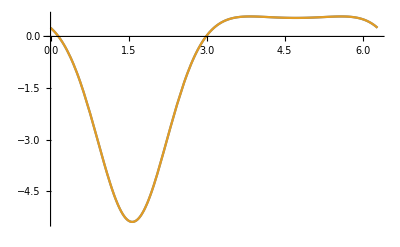

```mathematica
Plot[{t1,t2},{x,0,2Pi}]
```

```mathematica
nmax=5;
myt2=Pi/2;
jmax=10;
Plot[{pv10[1,1,theta1,myt2]Exp[Cos[theta1-myt2]],pv20[1,1,myt2,theta1]Exp[Cos[theta1-myt2]]},{theta1,0,2Pi}]
```

-Graphics-

```mathematica
■
```

■

```mathematica
(*nmax=1;jmax=10;
(*pv10[1,1,theta1,theta2]//Simplify
pv20[1,1,theta2,theta1]//Simplify*)*)
```

```mathematica
1/44236800(-81007533 Sin[theta1]-12402349 Sin[2 theta1-theta2]);
```

```mathematica
1/88473600(-162015066 Sin[theta1]-12402349 Sin[theta1-2 theta2]);
```

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

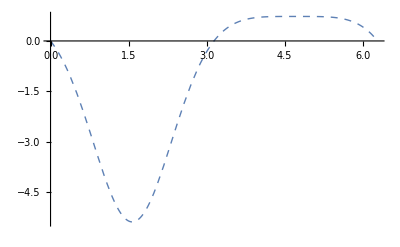

```mathematica
nmax=jmax=4;
myt2=Pi/2;
Plot[{pv10[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

Part::partd: Part specification Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is longer than depth of object.

ToExpression::notstrbox: Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partd: Part specification Flatten[$Failed, 1] ⟦ 2, 3 ⟧ is longer than depth of object.

ToExpression::notstrbox: Flatten[$Failed, 1] ⟦ 2, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 3 of Flatten[$Failed, 1] does not exist.

ToExpression::notstrbox: Flatten[$Failed, 1] ⟦ 3, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

Part::partw: Part 4 of Flatten[$Failed, 1] does not exist.

Part::partw: Part 5 of Flatten[$Failed, 1] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

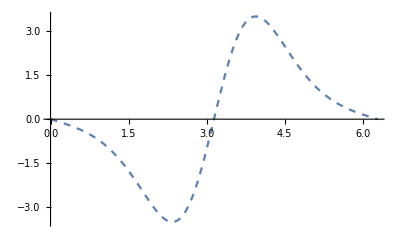

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv10[1,1,x,myt2]Exp[Cos[x-myt2]],pv20[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
(*myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv10[1,1,x,myt2],{x,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=2;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=3;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=4;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
nmax=jmax=5;plot[nmax]=Plot[pv10[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]];
plot[nmax+1]=Plot[pv20[1,1,myt2,x],{x,0,2Pi},PlotStyle->{Dashed,Thick}]
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]*)
```

## P11 and P21

```mathematica
Qx0=0;(*for coupling J is zero*)
Qx1=bmu^2+(bmu^2  BesselI[1,bJ])/BesselI[0,bJ]/.{bmu->1,bJ->1}//N
```

1.44639

```mathematica
nmax=jmax=1;
v11=pv11[1,1,theta1,theta2]//Simplify
v22=pv21[1,1,theta2,theta1]//Simplify
```

0.168421-0.05361 theta1+(-1.10181-0.15 Cos[2 theta1]) Cos[theta2] Sin[theta1]+Cos[theta1] (-1. Sin[theta1]+(-0.548195+0.15 Cos[2 theta1]) Sin[theta2])

Cos[theta2] (-1.00181-0.05 Cos[2 theta2]) Sin[theta1]+Cos[theta1] (-0.448195+0.05 Cos[2 theta2]) Sin[theta2]

π

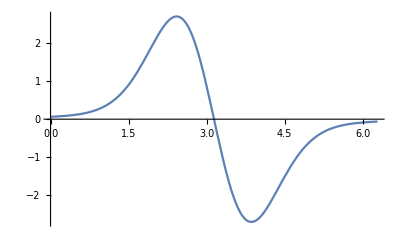

```mathematica
myt2=Pi
Plot[pv11[1,1,x,myt2]Exp[Cos[x-myt2]],{x,0,2Pi}]
```

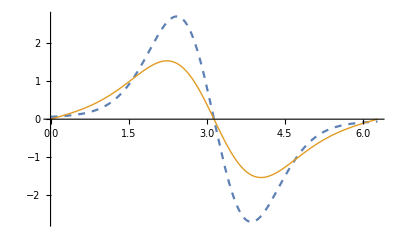

```mathematica
nmax=jmax=1;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

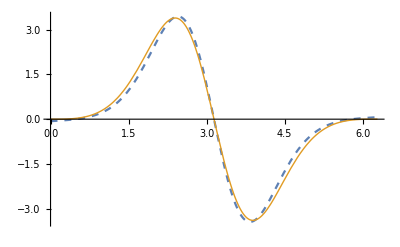

```mathematica
nmax=jmax=2;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

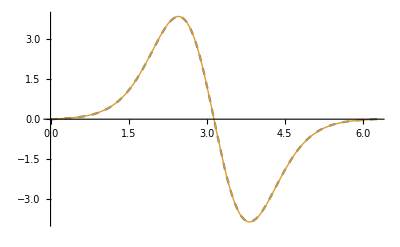

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

## test

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

-Graphics-

```mathematica
nmax=1;jmax=10;
(*pv11[1,1,theta1,theta2]//Simplify
pv21[1,1,theta2,theta1]//Simplify*)
```

```mathematica
1/44236800(-81007533 Sin[theta1]-12402349 Sin[2 theta1-theta2]);
```

```mathematica
1/88473600(-162015066 Sin[theta1]-12402349 Sin[theta1-2 theta2]);
```

```mathematica
colors={Red,Green,Blue,Orange,Black}
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 0, 1],RGBColor[1, 0.5, 0],GrayLevel[0]}

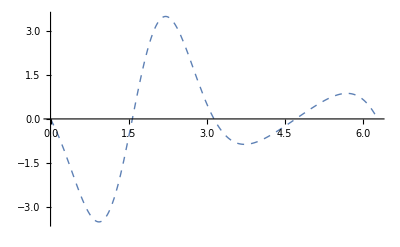

```mathematica
nmax=jmax=4;
myt2=Pi/2;
Plot[{pv11[1,1,theta2,myt2]Exp[Cos[theta2-myt2]]},{theta2,0,2Pi},PlotStyle->{Dashed,Thick}]
```

```mathematica
nmax=jmax=4;
myt2=Pi;
Plot[{pv11[1,1,x,myt2]Exp[Cos[x-myt2]],pv21[1,1,myt2,x]Exp[Cos[x-myt2]]},{x,0,2Pi},PlotStyle->{Dashed,Thick}]
```

-Graphics-

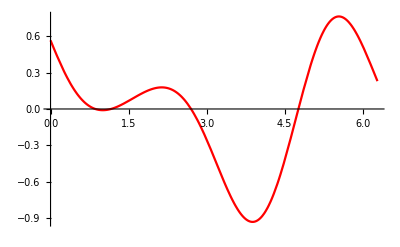

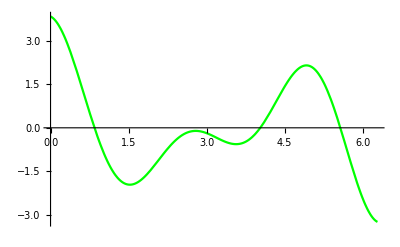

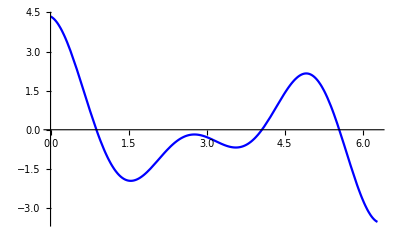

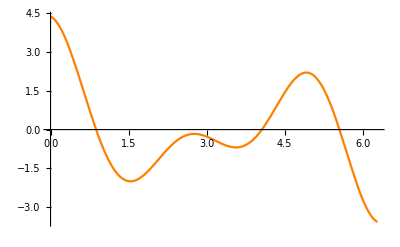

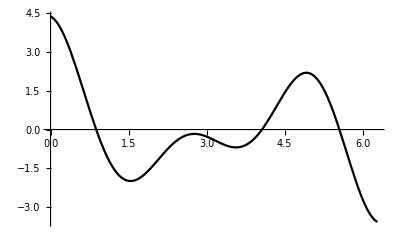

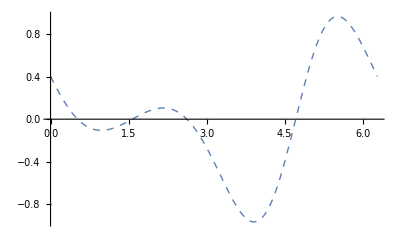

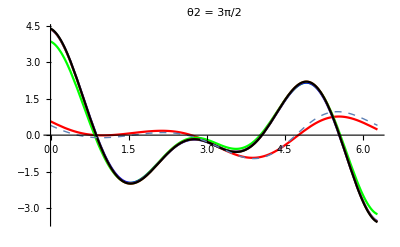

```mathematica
myt2=3Pi/2;
nmax=jmax=1;plot[nmax]=Plot[pv11[1,1,x,myt2],{x,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=2;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=3;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=4;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
nmax=jmax=5;plot[nmax]=Plot[pv11[1,1,theta1,myt2],{theta1,0,2Pi},PlotStyle->colors[[nmax]]]
plot[nmax+1]=Plot[pv21[1,1,myt2,x],{x,0,2Pi},PlotStyle->{Dashed,Thick}]
Show[Table[plot[nm],{nm,nmax+1}],PlotRange->All,PlotLabel->"θ2 = 3π/2"]
```

### get vEE from p11

```mathematica
nmax=1;jmax=0
pv10[1,1,theta1,theta2]
pv20[1,1,theta1,theta2]
pv11[1,1,theta1,theta2]
pv21[1,1,theta1,theta2]
```

0

0.-Sin[theta1]

Part::partd: Part specification Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is longer than depth of object.

ToExpression::notstrbox: Flatten[$Failed, 1] ⟦ 1, 3 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

$Failed Cos[theta2]-1. Sin[theta2]

-1.40238+0.44639 theta1-0.5 Cos[theta1] Sin[theta1]-Cos[theta2] Sin[theta1]

0.-Cos[theta1] Sin[theta2]

Note that P11 in Steven’s Sol is

```mathematica
-1/2 bmu^2 (Cos[theta1]+2 Cos[theta2]) Sin[theta1];
```

and we think it’s expression for vEE if we times p, However, it’s not!
P11 is actually A1 in the function below

```mathematica
A=A+A1*Ex+o(Ex^2);
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of A + A1\ Ex + Ex^2\ o.

where A = p v^E  and do expansion for p and v^E

```mathematica
p=p0+p1 Ex+ o(Ex^2);
v^E=vE+vEE*Ex+o(Ex^2);
```

Set::write: Tag Power in v^ⅇ is Protected.

so

```mathematica
p v^E  = (p0+p1 Ex+ o(Ex^2))(vE+vEE*Ex+o(Ex^2))=p0 vE + (p0 vEE+p1 vE)Ex + o(Ex^2);
```

Set::write: Tag Times in (Ex^2\ o + p0 + Ex\ p1)\ (Ex^2\ o + vE + Ex\ vEE) is Protected.

Set::write: Tag Times in (Ex^2\ o + p0 + Ex\ p1)\ v^ⅇ is Protected.

we know that

```mathematica
vE=-bmu Sin[theta1];
```

and p0 and p1 would be:

```mathematica
p=ⅇ^(bJ Cos[theta1-theta2]+bmu (Cos[theta1]+Cos[theta2]) Ex)/.bJ->0;
p0=Normal[Series[p,{Ex,0,0}]]
p1=(Normal[Series[p,{Ex,0,1}]]-p0)/Ex
```

1

bmu Cos[theta1]+bmu Cos[theta2]

and again

```mathematica
p11=-1/2 bmu^2 (Cos[theta1]+2 Cos[theta2]) Sin[theta1];
```

then we just need to solve for vEE

```mathematica
vE=-bmu Sin[theta1];
Solve[p0 vEE+p1 vE==p11,vEE]//Simplify
```

{{vEE→1/2 bmu^2 Cos[theta1] Sin[theta1]}}

Horray same with Our analytical result.

```mathematica
(**)
```